```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Secant

```mathematica
?SecantConnection
```

#### (* Circle*)

```mathematica
PlaneCurvePlot[{Cos[t/5],Sin[t/5]},{t,0,30,1},SecantConnection->{6,2},SecantLineStyle->{Hue[.4,.8,.7]},PlotParameterValue->True,DotStyle->{{PointSize[.02],Hue[.4,.8,.7]},{PointSize[.02],Hue[0]}},Ticks->None,PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* Archimedes' Spiral with secants *)

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,10 π,(10 π)/120},PlotDot->False,SecantConnection->{10,1},SecantLineStyle->Table[Hue[i],{i,0,1,1/120}],PlotRange->{{-22.3,22},{-22,22.3}},Axes->False,AspectRatio->1]
```

-Graphics-

#### (* Equiangular spiral with secants; "Nautilus" *)

```mathematica
PlaneCurvePlot[{ⅇ^(t Cot[80 °]) Cos[t],ⅇ^(t Cot[80 °]) Sin[t]},{t,0,6 π,(6 π)/70},PlotDot->False,SecantConnection->{9,1},Axes->False,AspectRatio->Automatic,PlotRange->{{-18,28},{-22,13}}]
```

-Graphics-

#### (* Trisectrix of Maclaurin with secants *)

```mathematica
PlaneCurvePlot[{(-3+t^2)/(1+t^2),(t (-3+t^2))/(1+t^2)},{t,-3,3,.1},SecantConnection->{20,1},PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* Folium of Descartes *)

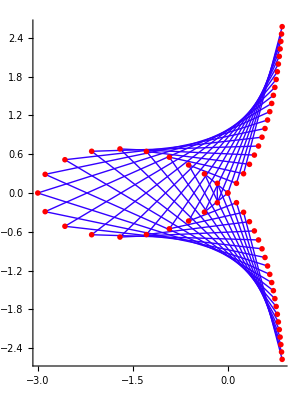

```mathematica
PlaneCurvePlot[{(3 (t^2-1))/(3 t^2+1),(3 t (t^2-1))/(3 t^2+1)},{t,-3,3,.1},PlotCurve->False,SecantConnection->{18,1},SecantLineStyle->{Hue[.7]},PlotRange->All,AspectRatio->Automatic]
```

#### (* Trochoid with colorful secants *)

```mathematica
PlaneCurvePlot[{t-2.2 Sin[t],1-2.2 Cos[t]},{t,0,3 2 π,.3},SecantConnection->{10,1},PlotDot->False,SecantLineStyle->Table[Hue[i],{i,0,1,1/62}],PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* 8 Curve; Lemniscate of Gerono *)

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t] Cos[t]},{t,0,6,.157},SecantConnection->{8,1},AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1,3/5,2/3] *)

```mathematica
PlaneCurvePlot[{2/3 Cos[(2 t)/3]+(2 Cos[t])/5,-2/3 Sin[(2 t)/3]+(2 Sin[t])/5},{t,0,5 2 π,(3 2 π)/100},SecantConnection->{40,1},Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 2/5, .13] *)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/5+0.13 Cos[(3 t)/2],(3 Sin[t])/5-0.13 Sin[(3 t)/2]},{t,0,3 2 π,(2 2 π)/(5 22)},SecantConnection->{5 3,1},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 5/14, 4/7] *)

```mathematica
PlaneCurvePlot[{(9 Cos[t])/14+4/7 Cos[(9 t)/5],(9 Sin[t])/14-4/7 Sin[(9 t)/5]},{t,0,6 2 π,(5 2 π)/140},SecantConnection->{14,1},Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid beauty, [1, 8/15, 8/15] *)

```mathematica
PlaneCurvePlot[{8/15 Cos[(7 t)/8]+(7 Cos[t])/15,-8/15 Sin[(7 t)/8]+(7 Sin[t])/15},{t,0,10 2 π,(8 2 π)/150},SecantConnection->{30,1},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-